# An Introduction to Mathematica (MM) (This is a title, style with an increased font size, Shortcut for title is (Alt + 1), Increase size is (Alt + “=”))

## Jesus Canez: (This is a subtitle style with and increased font size) September 2020 (The Year of the Devil)

## This is a sample Mathematica notebook to help get you started. (This is a subtitle style, shortcut is (Alt + 2)) Much of the functionality you will need in your class work is included here. Cells: (This is bolded, shortcut is (Ctrl + B) Cells are the building blocks of a Mathematica notebook. A cell is indicated by the brackets on the right hand side of the notebook. The default cell type is for executable code. To format this cell for text, we click on the cell’s bracket and select Format -> Style -> Subtitle

## Kernel: The Kernel evaluates code in a notebook on a cell by cell basis. To evaluate the cell below, Place the cursor in the cell below and press Shift-Enter. You will find the command under Evaluation -> Evaluate Cells. Also try Evaluate Notebook -- this evaluates all cells with executable code. (If MM won’t stop evaluating because of an error, stop it with evaluation -> Quit Kernel.)

```mathematica
(*some simple code *)
a = 3;
b = 2
Print["Hello World! a = ", a];
```

```mathematica
2
```

Hello World! a = 3

## In the code above , observe the following. -- A semicolon after input suppresses output. -- Note the structure of Print. Use often to avoid a silent program! -- An in-code comment is formed with (*...*) Let’s play a little to get a feeling for the input format. Plotting:

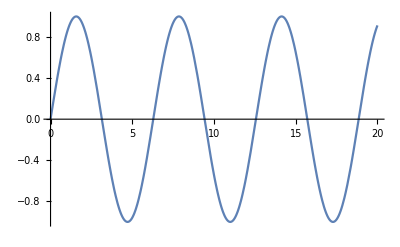

```mathematica
Plot[Sin[x],{x,0,20}]
```

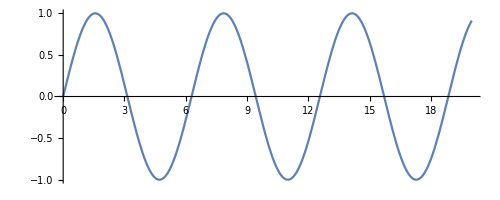

```mathematica
Plot[Sin[x], {x, 0, 20}, AspectRatio->Automatic]
```

```mathematica
Plot[Sin[x], {x, 0, 20}, AspectRatio->Full]
```

-Graphics-

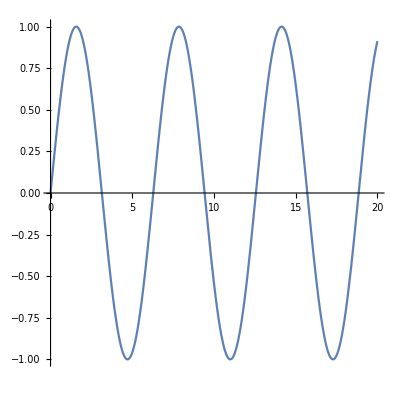

```mathematica
Plot[Sin[x], {x, 0, 20}, AspectRatio->1]
```

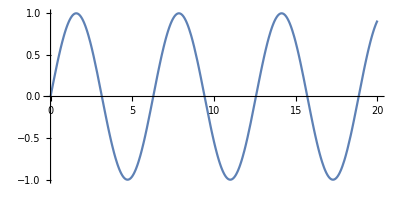

```mathematica
Plot[Sin[x], {x, 0, 20}, AspectRatio->1/2]
```

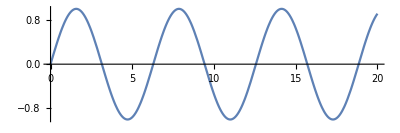

```mathematica
Plot[Sin[x], {x, 0, 20}, AspectRatio->1/3]
```

## If you don’t understand a command, use Help -> Find Selected Function (F1) or Help -> Wolfram Documentation to learn more about the input parameters. Go look up Plot. Here are some Examples for the Plot Function Documentation.

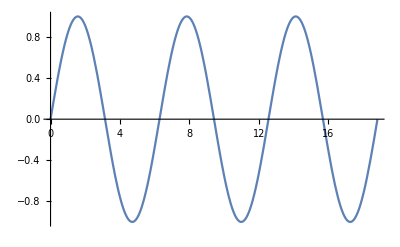

```mathematica
Plot[Sin[x], {x, 0, 6Pi}]
```

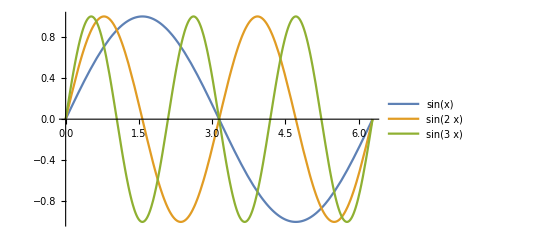

```mathematica
Plot[{Sin[x], Sin[2x], Sin[3x]},{x, 0, 2Pi}, PlotLegends->"Expressions"]
```

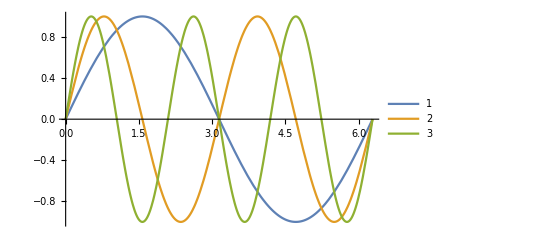

```mathematica
Plot[{Sin[x], Sin[2x], Sin[3x]},{x, 0, 2Pi}, PlotLegends->Automatic]
```

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2Pi}, PlotLabels->"Expressions"]
```

-Graphics-

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2Pi}, PlotLabels->"Expressions", Filling->Bottom]
```

-Graphics-

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 0, 2Pi}, PlotLabels->"Expressions", Filling-> {1 -> {2}}]
```

-Graphics-

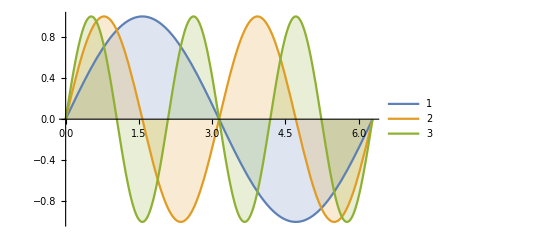

```mathematica
Plot[{Sin[x], Sin[2x], Sin[3x]},{x, 0, 2Pi}, PlotLegends->Automatic, Filling->Axis]
```

## Notice that MM routines begin with capital letters. Therefore, it is best if your variables and routines do not start with a capital letter.

## Manipulating: This next section we will take a look at the “Manipulate Function” Notice that it takes in a function and (a) variable(s) with a range. Format is as follows : Manipulate(Function name)[(open bracket) Plot[Sin[x * c(The variable that allows manipulation)], {x, 0, 2Pi}](What your manipulating), {c, 0, 2Pi}(The manipulator handle range)] You can also add multiple handles and adding addition al variables to the formula and ranges for those variables and you can see maniplator names and default values. You do this when you define the variable. Here is and example {{c, 1, “My Multiplier”}, 0, 2Pi} notice it is very similar to {c, 0, 2Pi} but we define the “c” input {c, 1, 2Pi} instead of just “c”. Here is and example of this below followed by another couple of fun interactive plots.

```mathematica
Manipulate[Plot[Sin[x*c], {x, 0, 2Pi}, Filling->Bottom], {{c, 1, "My Multiplier"}, 0, 2Pi}]
```

```mathematica
Manipulate[Plot[Sin[c*x], {x, 0,2Pi}], {c, 0, 2Pi}]
```

```mathematica
Manipulate[Plot[{Sin[x*c], Sin[2x*c], Sin[3x*c]},{x, 0, 2Pi}, PlotLegends->Automatic, Filling->Axis]  , {c, 0, 2Pi}]
```

## The “Manipulate” function needs Dynamic Updating Enabled. This setting is in the Evaluation menu. The default is enabled, but if MM gets hung-up, it might ask you if you want to disable it or wait. I recommend disable and then enable. This is good for security.

## Keep in mind that MM is very picky about notation; case matters, the type of bracket (square, curly, or round), etc. Variables are colored differently than pre-defined functions.

## Also Remember that the Help pages are notebooks too. This means that you can copy the commands from the Help pages directly into your notebook and they will work.

```mathematica
Sqrt[81] 
(* is not the same as *)
sqrt[81] (* MM  does not know what this is and will simply output this as text*)
variable1 = 1;
variable2 = 2;
variable3 = variable1 + variable2;
(* See how confusing the output gets when there isn't any text with the ouput. Try the following *)
Print["variable3 = variable1 + variable2 = ", variable3]
```

9

sqrt[81]

variable3 = variable1 + variable2 = 3

## Create a new cell by moving the mouse until the cursor becomes a horizontal bar and then click.

## Merge cells by selecting their brackets and use Cell -> Merge Cells. Try merging this cell with the previous one. The shortcut for this is (Shift + Ctrl + M)

## You can learn more about the basics of working with notebooks in the Document Center (Help -> Wolfram Documentation) and then selecting “Working in Notebooks.”

## 3D Plotting/Manipulating: Notice that the surface below looks very faceted as you move the slider, but when you leave the slider in one place for several seconds, the surface becomes smoother. Rotate the object by putting the cursor in the window with the surface, left-mouse click, and move the mouse. Zoom: Ctrl and Left-Mouse Click Translate: Shift and Left-Mouse Click

```mathematica
Manipulate[Plot3D[Sin[c * (x+y)], {x, -3, 3}, {y, -2, 3}, Filling->Bottom],{{c, 1, "Multiplier"}, 1, 5}]
```

## Functions: Things to notice in the function definitions below, input parameters are defined with a trailing underscore as so “x_”, but when referenced in the formula don’t include the underscore. Also, instead of an “=” sign we use the walrus “:=” and there is the “//N” which forces a numerical output instead of a possible intermediate representation.

```mathematica
(* Notice the difference between the output of these to variables *)
f[x_] := Sin[x^2 - Cos[x]] + x^2 //N; 
f2[x_] := Sin[x^2 - Cos[x]] + x^2;
g[x_] := 3x;
Print["This is with \"\\\\N\" = ", f[2]]
Print["This is without it = ", f2[2]]
```

This is with "\\N" = 3.04356

This is without it = 4+Sin[4-Cos[2]]

## You can also reference other cells variable meaning that variables declared in the same notebook are global.

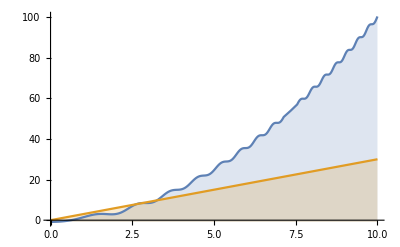

```mathematica
Plot[{f[x], g[x]}, {x, 0, 10}, Filling->Bottom]
```

## Subroutines: Not only all variable in a notebook are global but if you have other notebooks open with the same named variable you will be able to access those variable too. This is not defined behavior and may cause errors, so I bring it up so you can prevent possible issues. If you do want to specify a local variable, you will need to use the the command “Module” as we will see in the next section.

```mathematica
(* Defining my function here*)
mySubRoutine[x_, y_] := (
Print["mySubRoutine: input x = ", x, ", y = ", y];
a = x + y; (*  "Although "a" and "b" are in my fuction they are not local *)
 b = x * y;
Return[a];
);
a = 0; b = 0; x = 2; y = 3;
functionResult = mySubRoutine[x, y];
Print["The result of running my function with 2 and 3 is ", functionResult, " a = ", a, " and b = ", b];
Print["See I can still access a = ", a, " and b = ", b, " even outside my function."];
```

mySubRoutine: input x = 2, y = 3

The result of running my function with 2 and 3 is 5 a = 5 and b = 6

See I can still access a = 5 and b = 6 even outside my function.

## Experiment with functions by: * Removing the return statement;

```mathematica
testFunction1[x_] := (
i = x + 2;
j = x + 4;
);
testFunction2[x_] := (
i = x + 2;
j = x + 4;
Return[i + j];
);
myAnswer = testFunction1[1]; (* We expect to get 1 + 2 *)
myNextAnswer = testFunction2[1];
Print["What happens when we don't have a return statement? myAnswer = ", myAnswer];  
Print["What happens when we do have a return statement? myAnswer = ", myNextAnswer];
```

What happens when we don't have a return statement? myAnswer = Null

What happens when we do have a return statement? myAnswer = 8

## * Remove the semicolon(;) in the declaration of variables.

```mathematica
testFunction3[x_] := (
i = x + 2;(* the indentation changes too*)
j = x + 4;
Return[i + j];
);
myNextNextAnswer = testFunction3[1];
Print["What happens when we remove the semicolon from the declaration? myAnswer = ", myNextNextAnswer];
```

What happens when we remove the semicolon from the declaration? myAnswer = 8

## Module: As stated before all variables are global, if you do want a global variable then you need to use the “Module” command. Example below:

```mathematica
ff[x1_] :=(
Module[{localY = x1}, 
While[ localY > 0, localY = Log[localY]];
Return[localY];
]);
numHolder = ff[10]//N;
Print[numHolder];
Print[localY];
```

-0.181483

localY

## Notice that when we try to print localY that we don’t get the value of the variable defined in the function but instead we get “localY” which is what MM the name of the variable since MM doesn’t understand what it is.

## Lists and Tables: We will use lists and tables a lot in this class. Sometimes we will refer to them as arrays.

```mathematica
(* This is an example of a list, they can be printed in matrix form *)
```

```mathematica
ttt = {2, 3, 2, 6};
Print ["ttt = ", ttt," and ttt in Matrix form = ", MatrixForm[ttt] ];
```

ttt = {2,3,2,6} and ttt in matrix form = (2
3
2
6)

```mathematica
(* These are examplex of a tablex *)
(* input running from min to given max *)
Table[i^2, {i, 10}]
(* input running from specified min to max *)
Table[i^2, {i, 2, 10}]
(* input running from specified min to max in specified steps *)
sss = Table[i^2, {i,2, 10, 2}]
```

{1,4,9,16,25,36,49,64,81,100}

{4,9,16,25,36,49,64,81,100}

{4,16,36,64,100}

## We can use matrix from on these list too.

```mathematica
Print[MatrixForm[sss]];
```

(4
16
36
64
100)

## We can plot them too with ListPlot.

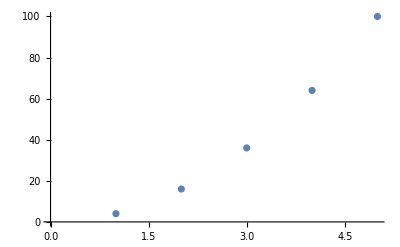

-Graphics3D-

```mathematica
ListPlot[sss]
(* This is a list of lists otherwise known as a 2D array *)
ThreeDList = {
{0,0,1},
{1,0,0},
{0,1,0}
};
ListPlot3D[ThreeDList, Mesh->All]
```

## By default, ListPlot plots over the integers Look up ListPlot in Help and modify the style of this plot. * Add list ttt to the plot * Join the points with a line * Change the color and point size (using PlotStyle)

{1,4,9,16,25,36,49,64,81,100}

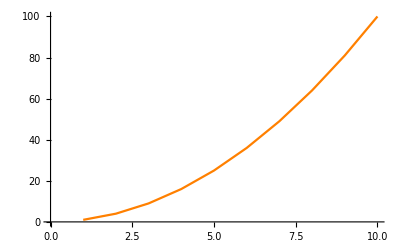

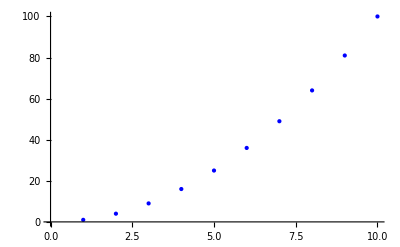

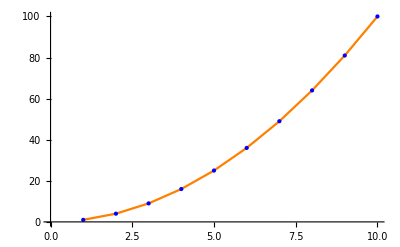

```mathematica
ttt = Table[i^2, {i, 10}];
Print[ttt];
plot1 = ListPlot[ttt, PlotStyle-> {Orange}, Joined->True]
plot2 = ListPlot[ttt, PlotStyle->{Blue, PointSize[Large]}]
Show[plot1, plot2]
```

## Points and Vectors: We will be working a lot with both of these in this class.

```mathematica
(* we are crating a list of 3D points with the Table function *)
```

```mathematica
points3D = Table[{i, i + 2, -i}, {i, 1, 5}];
Print["points3D =" ,points3D, " and in matrix form ", MatrixForm[points3D]];
```

points3D ={{1,3,-1},{2,4,-2},{3,5,-3},{4,6,-4},{5,7,-5}} and in matrix form (1 | 3 | -1
2 | 4 | -2
3 | 5 | -3
4 | 6 | -4
5 | 7 | -5)

## This is how you access an individual point from the a list of lists:

```mathematica
Print[points3D[[1]]];
Print[points3D[[2]]];
Print[points3D[[3]]];
Print[points3D[[3]]];
Print[points3D[[5]]];
```

{1,3,-1}

{2,4,-2}

{3,5,-3}

{3,5,-3}

{5,7,-5}

## This is how you access an individual element of the points from the a list of lists :

```mathematica
Print[points3D[[1,1]]];
Print[points3D[[1,2]]];
Print[points3D[[1,3]]];
```

1

3

-1

```mathematica
ccc = Table[{i, j, 4}, {i, 1, 3}, {j, 3, 4}];
Print["ccc = ", ccc, " and ccc in matrix form = ", MatrixForm[ccc]];
```

ccc = {{{1,3,4},{1,4,4}},{{2,3,4},{2,4,4}},{{3,3,4},{3,4,4}}} and ccc in matrix form = ((1
3
4) | (1
4
4)
(2
3
4) | (2
4
4)
(3
3
4) | (3
4
4))

## Notice that arrays in MM start at 1 and not 0 like most languages. Also notice that ccc is not a list of lists, instead it is a list of lists of lists, also known as a 3D array.

```mathematica
(* Accessing a list in 3D array *)
```

```mathematica
Print[ccc[[1]]];
```

{{1,3,4},{1,4,4}}

```mathematica
(* Accessing a list of lists in a 3D array *)
Print[ccc[[1,1]]];
```

{1,3,4}

```mathematica
(* Accessing a single element in a 3D array *)
Print[ccc[[1,1,2]]];
```

3

## Curves: Let us move on to curves, something that you will become very familiar with in this class.



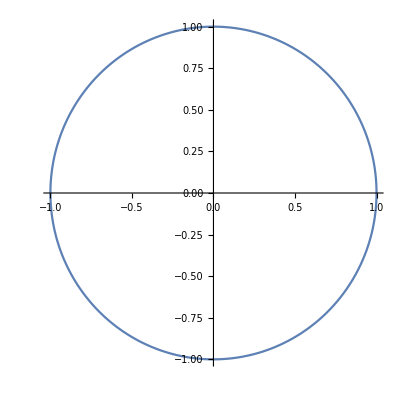

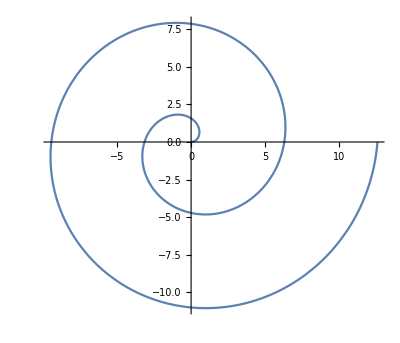

```mathematica
(* Parametric curve: Circle *)
myCurve[t_] := {Cos[t], Sin[t]};
ParametricPlot[{Cos[t], Sin[t]}, {t,0, 2Pi}]
ParametricPlot[{Sin[t], Cos[t]}, {t,0, 2Pi}]
ParametricPlot[{t * Cos[t], t * Sin[t]}, {t, 0, 4Pi}]
```

## Loops : In MM we have Do, form, and While loops which we saw when we worked with the “Module” command. Table also acts as a loop and saves the value in the table.

```mathematica
i = 0;
Do[(
j = i*3;
Print["i = ", i, ", j = ", j];),
{i, 0, 3}
];
```

i = 0, j = 0

i = 1, j = 3

i = 2, j = 6

i = 3, j = 9

```mathematica
(* bb holds some (x,y) points *)
bb = {
{0, 0},
{-2, 0},
{0, 2},
{2, 0.0}
};
(* calcualte the centroid of these four points *)
center = Sum[bb[[i]], {i, 1, 4}]/ 4;
(* find the distance of each point to the center *)
myDistanceTable = Table[Norm[bb[[i]] - center], {i, 1, 4}];
Print["Distance from bb_i to center = ", MatrixForm[myDistanceTable]];
```

Distance from bb_i to center = (0.5
2.06155
1.5
2.06155)

## Graphics Entities/Objects: MM has functions such as Graphics and PrametricPlot that return graphics objects. These are displayed by omitting a semicolon after the function or in the “Show” function. Both methods are demonstrated below. *** Important to know that you can NOT compute with graphics objects!***

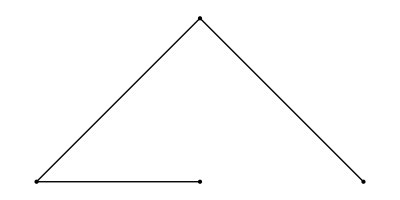

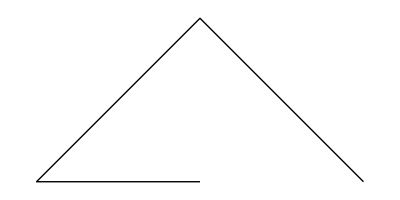

-Graphics-

```mathematica
myPoints = Graphics[{PointSize[Large], Point[bb]}];
myPolygon = Graphics[Line[bb]];
Show[{myPoints, myPolygon}]
myPolygon
myPoints
```

## Global Variables: As discussed before, by default all the variables are global. If you want to specify a local variable in a routine, you will need to use the “Module” command. To clear or remove global variables, at the start of your program add the command “Clear[“Global’*”];” or “Remove[“Global’*”];”, respectively. (When you run the next three cells with Evaluate all cells, notice that “check globals” will turn blue (or whatever your undefined variable color is defined as.) Be aware that variables are shared across open notebooks!! This can cause problems if two notebooks are running a Manipulate environment with the same variables.

```mathematica
(* execute this cell *)
checkglobals = 1;
Print["Global variables include: "];
Names["Global`*"]
```

Global variables include:

{b,bb,ccc,center,checkglobals,Cost,f,ff,i,j,localX,localX$,localY,localY$,myCurve,myDistanceTable,myNextNextAnswer,myPoints,myPolygon,myPolygons,numHolder,plot1,plot2,points3D,polygon,sss,t,testFunction3,ThreeDList,ttt,x,x0,x1,x1$,x$,$16,$17,$18,$19,$20,$21,$22,$23,$24,$25}

```mathematica
(* Now execute this cell *)
(*This clears the variable references completely*)
Clear["Global`*"];
```

```mathematica
(* Variables exist but no value assigned *)
Print["Global variables after Clear include: "];
Names["Global`*"]
```

Global variables after Clear include:

{b,bb,ccc,center,checkglobals,Cost,f,ff,i,j,localX,localX$,localY,localY$,myCurve,myDistanceTable,myNextNextAnswer,myPoints,myPolygon,myPolygons,numHolder,plot1,plot2,points3D,polygon,sss,t,testFunction3,ThreeDList,ttt,x,x0,x1,x1$,x$,$16,$17,$18,$19,$20,$21,$22,$23,$24,$25}

```mathematica
(* Now execute this cell *)
(*This removes the variable references completely*)
Remove["Global`*"];

(*No variables...*)
Print["Global variables after Remove include: "];
Names["Global`*"]
```

Global variables after Remove include:

{}